```mathematica
λ[{a_,b_}][p_]:=((a-p).(a-b))/((a-b).(a-b))
LineIntersectionPoint[{{a_,b_},{c_,d_}}]:=(Det[{a,b}] (c-d)-Det[{c,d}] (a-b))/Det[{a-b,c-d}]
SegmentIntersectionQ[{p1:{a_,b_},p2:{c_,d_}}]:=
If[Det[{a-b,c-d}]==0,False,
Module[{p=LineIntersectionPoint[{p1,p2}]},0≤λ[p1][p]≤1&&0≤λ[p2][p]≤1]]
```

```mathematica
SegmentIntersectionQ[{{{6,5},{-6,2}},{{-3,4},{6,-1}}}]
```

True

```mathematica
LineIntersectionPoint[{{{6,5},{-6,2}},{{-3,4},{6,-1}}}]
```

{-42/29,91/29}

```mathematica
abnsegs[{a_,b_,c_,d_},{e_,f_,g_,h_}]:=Piecewise[{{Piecewise[{{Norm[Cross[{c-a,d-b,0},{g-e,h-f,0}]], Length[DeleteDuplicates[{{a,b},{c,d},{e,f},{g,h}}]]<4}, {Block[{pt=LineIntersectionPoint[{{{a,b},{c,d}},{{e,f},{g,h}}}]},Norm[Cross[Join[{a,b}-pt,{0}],Join[{e,f}-pt,{0}]]]+Norm[Cross[Join[{c,d}-pt,{0}],Join[{g,h}-pt,{0}]]]], Length[DeleteDuplicates[{{a,b},{c,d},{e,f},{g,h}}]]≥4}}], SegmentIntersectionQ[{{{a,b},{c,d}},{{e,f},{g,h}}}]==True}, {Norm[{c-a,d-b}]*Norm[{e-a,f-b}], SegmentIntersectionQ[{{{a,b},{c,d}},{{e,f},{g,h}}}]==False}}]
```

```mathematica
Join[{1,2},{0}]
```

{1,2,0}

```mathematica
matar[x_]:=Select[Flatten[Block[{l=Length[x]^2},Block[{l2=
Block[{l1=Table[First[Position[x,i]],{i,1,l}]},Table[{First[l1[[i]]],Last[l1[[i]]],First[l1[[i+1]]],Last[l1[[i+1]]]},{i,1,l-1}]]},
Table[Table[abnsegs[l2[[i]],l2[[j]]],{i,1,j}],{j,1,l-1}]
]]],#>0&]
matar[({{4, 9, 2}, {3, 5, 7}, {8, 1, 6}})]
Total[%]
```

{3,√10,2,5,5/3,1,5/3,√10,1,2,√5,2 √5,√5,4,1,5/3,√5,2,√10,5/3,2,√5,5/3,1,5/3,2,2,3}

41+6 √5+3 √10

```mathematica
First[Last[GM[({{4, 9, 2}, {3, 5, 7}, {8, 1, 6}})]]]
```

```mathematica
mmt[x_]:=Block[{l1=matar[x]},{Min[l1],Max[l1],Total[l1]}]
```

```mathematica
Timing[Map[{#,First[Last[GM[Last[#]]]]}&,Sort[Table[Block[{m=Partition[Permute[Range[9],RandomPermutation[9]],3]},{mmt[m],m}],{i,1,1000}],First[#1][[3]]<First[#2][[3]]&]]]
```

```mathematica
ef[{x_,m_}]:=Block[{m2=Partition[Permute[Range[16],RandomPermutation[16]],4]},Block[{x2=Total[matar[m2]]},Piecewise[{{{x,m}, x>x2}, {{x2,m2}, x≤x2}}]]]
```

```mathematica
Timing[Nest[ef,{41+6 √5+3 √10,{{4,9,2},{3,5,7},{8,1,6}}},100000]]
```

{3173.46,{287873/1155+18 √2+14 √5+18 √10+14 √13+11 √26+4 √65+3 √130,{{2,4,8,11},{10,16,14,6},{15,1,12,13},{7,9,3,5}}}}

```mathematica
Last[Last[%]]
```

{{2,4,8,11},{10,16,14,6},{15,1,12,13},{7,9,3,5}}

```mathematica
{GM[%],matuni[%]}
```

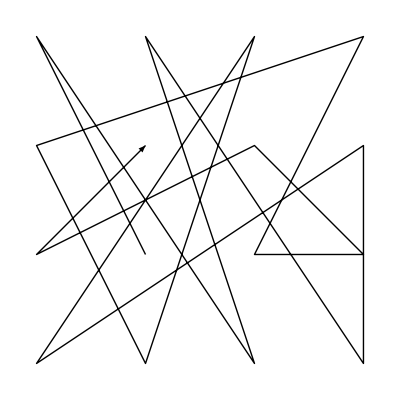
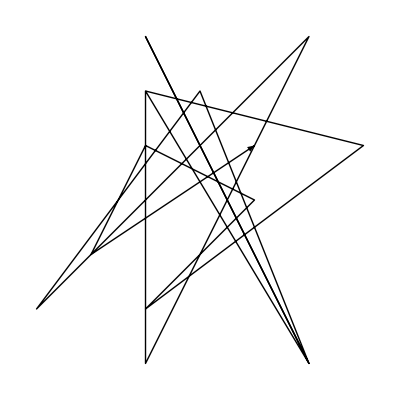
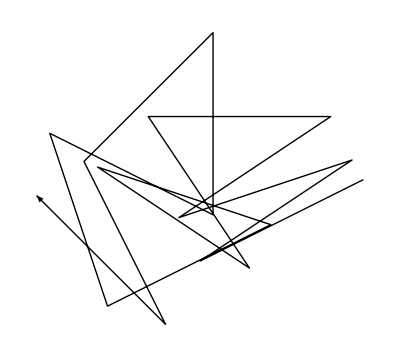
```mathematica
{{({{2, 4, 8, 11}, {10, 16, 14, 6}, {15, 1, 12, 13}, {7, 9, 3, 5}}),{-Graphics-,{{-1,2},{2,-3},{-1,3},{2,-3},{0,2},{-3,-2},{2,3},{-1,-3},{-1,2},{3,1},{-1,-2},{1,0},{-1,1},{-2,-1},{1,1}},-Graphics-}},-Graphics-}
```

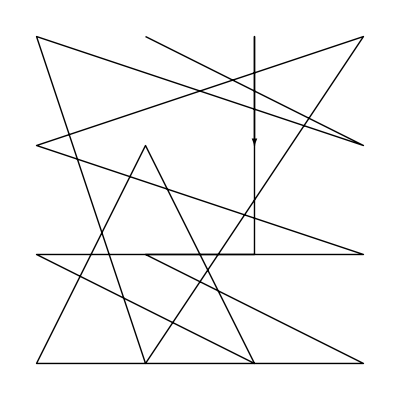
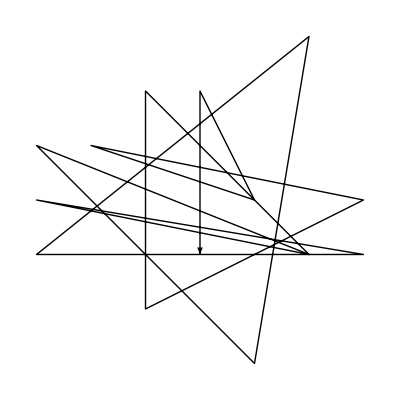
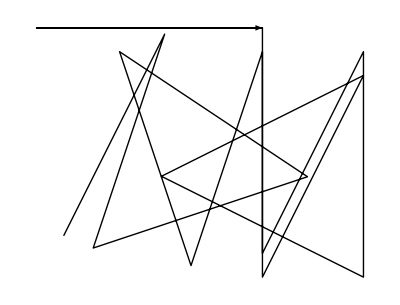
```mathematica
{{({{3, 1, 15, 5}, {6, 10, 16, 2}, {8, 13, 14, 7}, {11, 4, 9, 12}}),{-Graphics-,{{2,-1},{-3,1},{1,-3},{2,3},{-3,-1},{3,-1},{-3,0},{2,-1},{-1,2},{-1,-2},{3,0},{-2,1},{1,0},{0,2},{0,-1}},-Graphics-}},-Graphics-}
```

```mathematica
{1236.3449660000006,{12698783/60060+44 √2+32 √5+22 √10+9 √13+7 √26+3 √65+2 √130,{{7,15,2,4},{3,16,12,14},{5,11,13,9},{10,8,6,1}}}}
```

```mathematica
{900.1184980000007,{496/3+47 √2+48 √5+34 √10+10 √13+3 √26+3 √130,{{5,1,15,4},{9,12,14,13},{10,16,11,3},{2,7,8,6}}}}
```

```mathematica
{323.48179300000083,{29674/165+46 √2+42 √5+25 √10+9 √13+2 √26+2 √65+5 √130,{{3,13,1,8},{12,6,10,4},{11,9,16,14},{5,2,15,7}}}}
```

```mathematica
{28.658536000000822,{40993/210+56 √2+38 √5+34 √10+12 √13+2 √26+√65,{{3,14,15,8},{13,9,12,5},{11,6,16,1},{2,4,10,7}}}}
```

```mathematica
{0.3082169999997859,{4988/35+39 √2+31 √5+22 √10+10 √13+7 √26+4 √65+√130,{{2,8,10,7},{11,13,9,12},{16,15,6,1},{5,4,14,3}}}}
```

```mathematica
{First[%],Last[%]}
```

{{79/3+5 √2+4 √5,{{9,7,4},{5,8,3},{6,1,2}}},{641/15+4 √2+13 √5+3 √10,{{2,6,4},{8,9,1},{7,3,5}}}}

```mathematica
Map[Last,%]
```

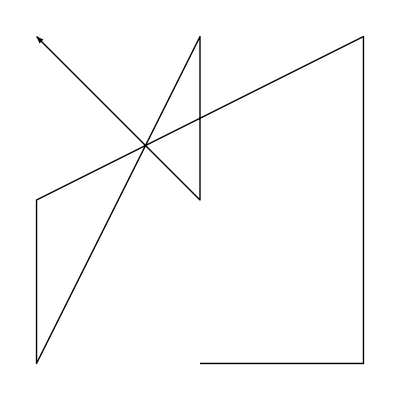
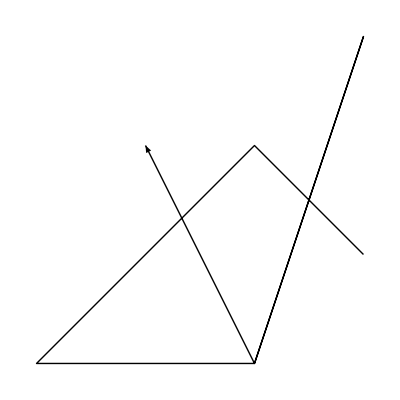
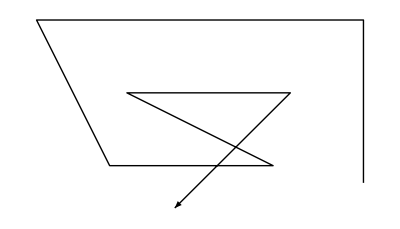
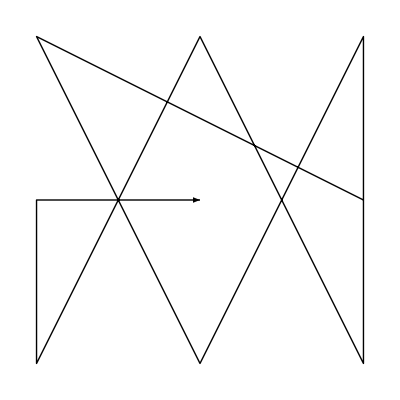
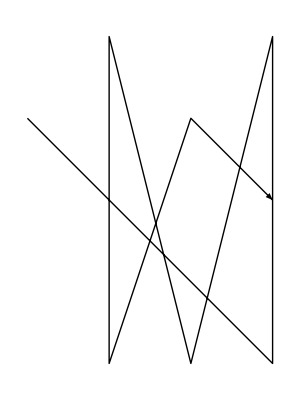
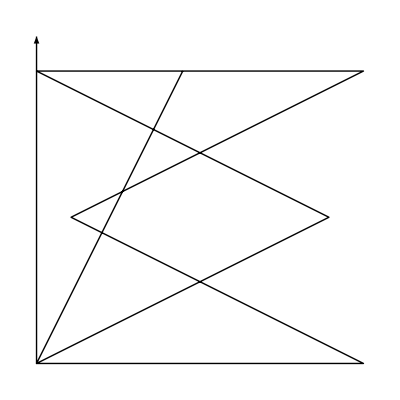
{{(9 | 7 | 4
5 | 8 | 3
6 | 1 | 2),{-Graphics-,{{1,0},{0,1},{0,1},{-2,-1},{0,-1},{1,2},{0,-1},{-1,1}},-Graphics-}},-Graphics-}
{{(2 | 6 | 4
8 | 9 | 1
7 | 3 | 5),{-Graphics-,{{-2,1},{1,-2},{1,2},{0,-2},{-1,2},{-1,-2},{0,1},{1,0}},-Graphics-}},-Graphics-}

```mathematica
Map[{GM[#],matuni[#]}&,{{{9,7,4},{5,8,3},{6,1,2}},{{2,6,4},{8,9,1},{7,3,5}}}]//Column
```

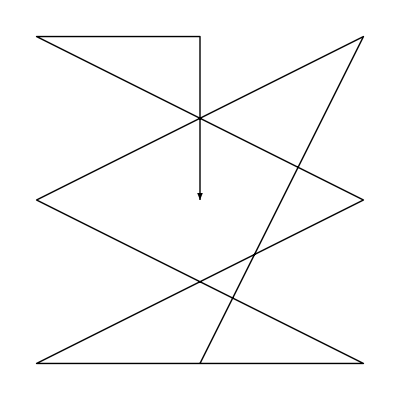
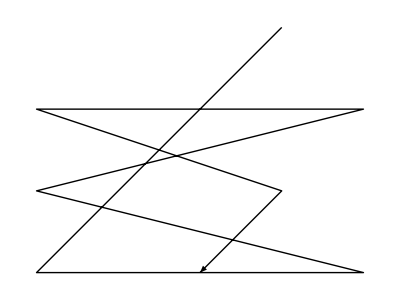
{(7 | 8 | 2
3 | 9 | 6
5 | 1 | 4),{-Graphics-,{{1,2},{-2,-1},{2,-1},{-2,0},{2,1},{-2,1},{1,0},{0,-1}},-Graphics-}}

```mathematica
GM[{{7,8,2},{3,9,6},{5,1,4}}]
```

```mathematica
{7.459699000000228,{109/3+7 √2+11 √5+4 √10,{{2,4,1},{8,9,3},{6,7,5}}}}
```

```mathematica
{7.47543399999995,{641/15+4 √2+13 √5+3 √10,{{5,3,7},{1,9,8},{4,6,2}}}}
```

```mathematica
{7.489700999999968,{233/5+4 √2+11 √5+2 √10,{{5,8,3},{1,9,7},{6,4,2}}}}
```

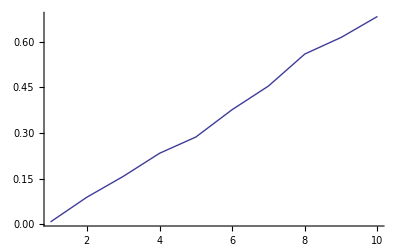

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
Length[{{3,2,1,3},{1,3,2,1},{2,1,1,1},{1,1,2,2},{2,2,3,3},{3,3,2,3},{2,3,3,1},{3,1,1,2}}]
```

8

```mathematica
1==2||3==3
```

True

```mathematica
Norm[{1,1}]
```

√2

```mathematica
Piecewise[{{1, True}, {2, True}}]
```

1

```mathematica
feoj[{a_,b_,c_,d_},{e_,f_,g_,h_}]:=
Piecewise[{{LineIntersectionPoint[{{{a,b},{c,d}},{{e,f},{g,h}}}], SegmentIntersectionQ[{{{a,b},{c,d}},{{e,f},{g,h}}}]==True}, {{0,0}, SegmentIntersectionQ[{{{a,b},{c,d}},{{e,f},{g,h}}}]==False}}]
```

```mathematica
fjo={{1,1,1,1},{1,1,1,2},{1,2,1,2},{1,1,1,3},{1,2,1,3},{1,3,1,3},{1,1,2,1},{1,2,2,1},{1,3,2,1},{2,1,2,1},{1,1,2,2},{1,2,2,2},{1,3,2,2},{2,1,2,2},{2,2,2,2},{1,1,2,3},{1,2,2,3},{1,3,2,3},{2,1,2,3},{2,2,2,3},{2,3,2,3},{1,1,3,1},{1,2,3,1},{1,3,3,1},{2,1,3,1},{2,2,3,1},{2,3,3,1},{3,1,3,1},{1,1,3,2},{1,2,3,2},{1,3,3,2},{2,1,3,2},{2,2,3,2},{2,3,3,2},{3,1,3,2},{3,2,3,2},{1,1,3,3},{1,2,3,3},{1,3,3,3},{2,1,3,3},{2,2,3,3},{2,3,3,3},{3,1,3,3},{3,2,3,3},{3,3,3,3}};
Select[DeleteDuplicates[Partition[Flatten[Table[Table[feoj[fjo[[i]],fjo[[j]]],{i,1,j}],{j,1,45}]],2]],Total[#]≠0&]
```

{{1,1},{1,2},{2,1},{1,3},{3/2,3/2},{5/3,5/3},{3/2,2},{2,2},{4/3,5/3},{5/3,7/3},{4/3,7/3},{3/2,5/2},{2,3},{2,3/2},{7/5,9/5},{3,1},{5/3,4/3},{9/5,7/5},{7/3,5/3},{13/5,9/5},{5/2,2},{3,2},{9/5,13/5},{5/3,8/3},{2,5/2},{7/3,7/3},{7/3,4/3},{5/2,3/2},{8/3,5/3},{5/2,5/2},{7/5,11/5},{11/5,13/5},{7/3,8/3},{3,3},{11/5,7/5},{13/5,11/5},{8/3,7/3}}

```mathematica
Table[Out[138][[i]]->ToExpression[StringJoin["v",ToString[i]]],{i,1,37}]
```

{{1,1}→v1,{1,2}→v2,{2,1}→v3,{1,3}→v4,{3/2,3/2}→v5,{5/3,5/3}→v6,{3/2,2}→v7,{2,2}→v8,{4/3,5/3}→v9,{5/3,7/3}→v10,{4/3,7/3}→v11,{3/2,5/2}→v12,{2,3}→v13,{2,3/2}→v14,{7/5,9/5}→v15,{3,1}→v16,{5/3,4/3}→v17,{9/5,7/5}→v18,{7/3,5/3}→v19,{13/5,9/5}→v20,{5/2,2}→v21,{3,2}→v22,{9/5,13/5}→v23,{5/3,8/3}→v24,{2,5/2}→v25,{7/3,7/3}→v26,{7/3,4/3}→v27,{5/2,3/2}→v28,{8/3,5/3}→v29,{5/2,5/2}→v30,{7/5,11/5}→v31,{11/5,13/5}→v32,{7/3,8/3}→v33,{3,3}→v34,{11/5,7/5}→v35,{13/5,11/5}→v36,{8/3,7/3}→v37}

```mathematica
pointsonline=Select[Table[Select[DeleteDuplicates[Partition[Flatten[Table[feoj[fjo[[i]],fjo[[j]]],{j,1,45}]],2]],Total[#]≠0&],{i,1,45}],Length[#]>0&];
osih[list_]:=Partition[Flatten[Table[Table[{list[[i]],list[[j]]},{i,1,j}],{j,1,Length[list]}]],2];
```

```mathematica
ReplaceAll[pointsonline,{{1,1}->v1,{1,2}->v2,{2,1}->v3,{1,3}->v4,{3/2,3/2}->v5,{5/3,5/3}->v6,{3/2,2}->v7,{2,2}->v8,{4/3,5/3}->v9,{5/3,7/3}->v10,{4/3,7/3}->v11,{3/2,5/2}->v12,{2,3}->v13,{2,3/2}->v14,{7/5,9/5}->v15,{3,1}->v16,{5/3,4/3}->v17,{9/5,7/5}->v18,{7/3,5/3}->v19,{13/5,9/5}->v20,{5/2,2}->v21,{3,2}->v22,{9/5,13/5}->v23,{5/3,8/3}->v24,{2,5/2}->v25,{7/3,7/3}->v26,{7/3,4/3}->v27,{5/2,3/2}->v28,{8/3,5/3}->v29,{5/2,5/2}->v30,{7/5,11/5}->v31,{11/5,13/5}->v32,{7/3,8/3}->v33,{3,3}->v34,{11/5,7/5}->v35,{13/5,11/5}->v36,{8/3,7/3}->v37}]
```

{{v1,v2},{v1,v2,v4},{v2,v4},{v1,v3},{v2,v3,v5,v9,v17},{v4,v3,v6,v7,v11,v18,v31},{v1,v5,v6,v8},{v2,v7,v8},{v4,v8,v10,v12},{v3,v8,v14},{v1,v9,v7,v10,v13,v15,v23},{v2,v11,v12,v13,v24},{v4,v13},{v3,v8,v13,v14,v25},{v8,v13,v25},{v1,v3,v16},{v2,v6,v14,v15,v16,v27,v35},{v4,v8,v10,v12,v16,v19,v28},{v3,v16},{v8,v16,v19,v28},{v13,v16,v20,v21,v26,v29,v32},{v1,v17,v18,v14,v19,v20,v22},{v2,v7,v8,v21,v22},{v4,v23,v24,v25,v26,v22,v36},{v3,v27,v28,v29,v22},{v8,v21,v22},{v13,v22,v30,v33,v37},{v16,v22},{v1,v5,v6,v8,v26,v30,v34},{v2,v31,v10,v25,v32,v33,v34},{v4,v13,v34},{v3,v35,v19,v21,v36,v37,v34},{v8,v26,v30,v34},{v13,v34},{v16,v22,v34},{v22,v34}}

```mathematica
Graph[Map[First[#]<->Last[#]&,Select[DeleteDuplicates[DeleteDuplicates[Partition[Flatten[osih[%]],2]],#1[[1]]==#2[[2]]&&#2[[1]]==#1[[2]]&],Length[DeleteDuplicates[#]]>1&]]]
```

-Graphics-

```mathematica
Table[Map[First,Position[pointsonline,i]],{i,Out[130]}]
```

{{2,4,7,11,16,22,29,37},{2,4,5,8,12,17,23,30,38},{7,8,9,14,19,22,25,32,40},{4,5,9,13,18,24,31,39},{8,11,37},{9,11,23,37},{9,12,16,30},{11,12,13,14,19,20,24,26,30,33,37,41},{8,16},{13,16,24,38},{9,17},{13,17,24},{16,17,18,19,20,27,34,39,42},{14,19,23,29},{16,23},{22,23,24,25,26,27,35,43},{8,29},{9,29},{24,26,29,40},{27,29},{27,30,33,40},{29,30,31,32,33,34,35,43,44},{16,31},{17,31},{19,20,31,38},{27,31,37,41},{23,32},{24,26,32},{27,32},{34,37,41},{9,38},{27,38},{34,38},{37,38,39,40,41,42,43,44},{23,40},{31,40},{34,40}}

```mathematica
Map[First,Position[{{},{{1,1},{1,2}},{},{{1,1},{1,2},{1,3}},{{1,2},{1,3}},{},{{1,1},{2,1}},{{1,2},{2,1},{3/2,3/2},{4/3,5/3},{5/3,4/3}},{{1,3},{2,1},{5/3,5/3},{3/2,2},{4/3,7/3},{9/5,7/5},{7/5,11/5}},{},{{1,1},{3/2,3/2},{5/3,5/3},{2,2}},{{1,2},{3/2,2},{2,2}},{{1,3},{2,2},{5/3,7/3},{3/2,5/2}},{{2,1},{2,2},{2,3/2}},{},{{1,1},{4/3,5/3},{3/2,2},{5/3,7/3},{2,3},{7/5,9/5},{9/5,13/5}},{{1,2},{4/3,7/3},{3/2,5/2},{2,3},{5/3,8/3}},{{1,3},{2,3}},{{2,1},{2,2},{2,3},{2,3/2},{2,5/2}},{{2,2},{2,3},{2,5/2}},{},{{1,1},{2,1},{3,1}},{{1,2},{5/3,5/3},{2,3/2},{7/5,9/5},{3,1},{7/3,4/3},{11/5,7/5}},{{1,3},{2,2},{5/3,7/3},{3/2,5/2},{3,1},{7/3,5/3},{5/2,3/2}},{{2,1},{3,1}},{{2,2},{3,1},{7/3,5/3},{5/2,3/2}},{{2,3},{3,1},{13/5,9/5},{5/2,2},{7/3,7/3},{8/3,5/3},{11/5,13/5}},{},{{1,1},{5/3,4/3},{9/5,7/5},{2,3/2},{7/3,5/3},{13/5,9/5},{3,2}},{{1,2},{3/2,2},{2,2},{5/2,2},{3,2}},{{1,3},{9/5,13/5},{5/3,8/3},{2,5/2},{7/3,7/3},{3,2},{13/5,11/5}},{{2,1},{7/3,4/3},{5/2,3/2},{8/3,5/3},{3,2}},{{2,2},{5/2,2},{3,2}},{{2,3},{3,2},{5/2,5/2},{7/3,8/3},{8/3,7/3}},{{3,1},{3,2}},{},{{1,1},{3/2,3/2},{5/3,5/3},{2,2},{7/3,7/3},{5/2,5/2},{3,3}},{{1,2},{7/5,11/5},{5/3,7/3},{2,5/2},{11/5,13/5},{7/3,8/3},{3,3}},{{1,3},{2,3},{3,3}},{{2,1},{11/5,7/5},{7/3,5/3},{5/2,2},{13/5,11/5},{8/3,7/3},{3,3}},{{2,2},{7/3,7/3},{5/2,5/2},{3,3}},{{2,3},{3,3}},{{3,1},{3,2},{3,3}},{{3,2},{3,3}},{}},{3,2}]]
```

{29,30,31,32,33,34,35,43,44}

```mathematica
tf[x_]:=Piecewise[{{1, x==True}, {0, x==False}}]
ewhi[{a_,b_,c_,d_},{e_,f_,g_,h_}]:=tf[SegmentIntersectionQ[{{{a,b},{c,d}},{{e,f},{g,h}}}]]

linmat[n_]:=Block[{l2=Partition[Flatten[Block[{l1=Partition[Flatten[Table[{a,b},{a,1,n},{b,1,n}]],2]},Table[Table[{l1[[i]],l1[[j]]},{i,1,j}],{j,1,n^2}]]],4]},{l2,Monitor[Table[ewhi[l2[[i]],l2[[j]]],{i,1,Length[l2]},{j,1,Length[l2]}],{i,j}]}]
```

```mathematica
linmat[3]
ArrayPlot[Last[%]]
```

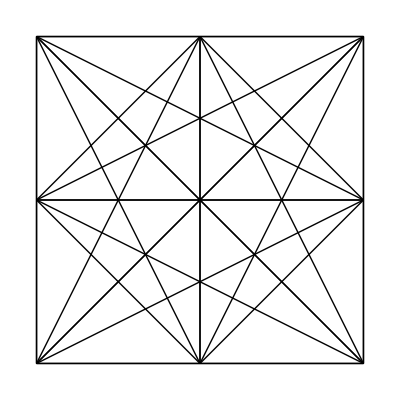

```mathematica
Graphics[{Line[{{{1,1},{1,1}}}],Line[{{{1,1},{1,2}}}],Line[{{{1,2},{1,2}}}],Line[{{{1,1},{1,3}}}],Line[{{{1,2},{1,3}}}],Line[{{{1,3},{1,3}}}],Line[{{{1,1},{2,1}}}],Line[{{{1,2},{2,1}}}],Line[{{{1,3},{2,1}}}],Line[{{{2,1},{2,1}}}],Line[{{{1,1},{2,2}}}],Line[{{{1,2},{2,2}}}],Line[{{{1,3},{2,2}}}],Line[{{{2,1},{2,2}}}],Line[{{{2,2},{2,2}}}],Line[{{{1,1},{2,3}}}],Line[{{{1,2},{2,3}}}],Line[{{{1,3},{2,3}}}],Line[{{{2,1},{2,3}}}],Line[{{{2,2},{2,3}}}],Line[{{{2,3},{2,3}}}],Line[{{{1,1},{3,1}}}],Line[{{{1,2},{3,1}}}],Line[{{{1,3},{3,1}}}],Line[{{{2,1},{3,1}}}],Line[{{{2,2},{3,1}}}],Line[{{{2,3},{3,1}}}],Line[{{{3,1},{3,1}}}],Line[{{{1,1},{3,2}}}],Line[{{{1,2},{3,2}}}],Line[{{{1,3},{3,2}}}],Line[{{{2,1},{3,2}}}],Line[{{{2,2},{3,2}}}],Line[{{{2,3},{3,2}}}],Line[{{{3,1},{3,2}}}],Line[{{{3,2},{3,2}}}],Line[{{{1,1},{3,3}}}],Line[{{{1,2},{3,3}}}],Line[{{{1,3},{3,3}}}],Line[{{{2,1},{3,3}}}],Line[{{{2,2},{3,3}}}],Line[{{{2,3},{3,3}}}],Line[{{{3,1},{3,3}}}],Line[{{{3,2},{3,3}}}],Line[{{{3,3},{3,3}}}]}]
```

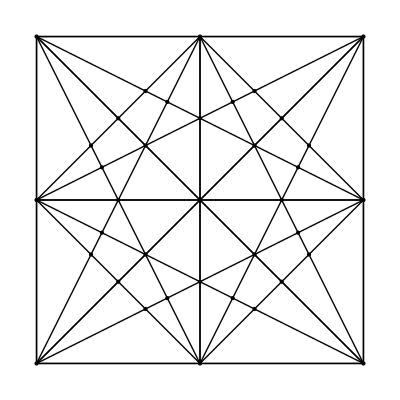

```mathematica
Graphics[{{PointSize[Large],Point[{{1,1},{1,2},{2,1},{1,3},{3/2,3/2},{5/3,5/3},{3/2,2},{2,2},{4/3,5/3},{5/3,7/3},{4/3,7/3},{3/2,5/2},{2,3},{2,3/2},{7/5,9/5},{3,1},{5/3,4/3},{9/5,7/5},{7/3,5/3},{13/5,9/5},{5/2,2},{3,2},{9/5,13/5},{5/3,8/3},{2,5/2},{7/3,7/3},{7/3,4/3},{5/2,3/2},{8/3,5/3},{5/2,5/2},{7/5,11/5},{11/5,13/5},{7/3,8/3},{3,3},{11/5,7/5},{13/5,11/5},{8/3,7/3}}]},Line[{{{1,1},{1,1}}}],Line[{{{1,1},{1,2}}}],Line[{{{1,2},{1,2}}}],Line[{{{1,1},{1,3}}}],Line[{{{1,2},{1,3}}}],Line[{{{1,3},{1,3}}}],Line[{{{1,1},{2,1}}}],Line[{{{1,2},{2,1}}}],Line[{{{1,3},{2,1}}}],Line[{{{2,1},{2,1}}}],Line[{{{1,1},{2,2}}}],Line[{{{1,2},{2,2}}}],Line[{{{1,3},{2,2}}}],Line[{{{2,1},{2,2}}}],Line[{{{2,2},{2,2}}}],Line[{{{1,1},{2,3}}}],Line[{{{1,2},{2,3}}}],Line[{{{1,3},{2,3}}}],Line[{{{2,1},{2,3}}}],Line[{{{2,2},{2,3}}}],Line[{{{2,3},{2,3}}}],Line[{{{1,1},{3,1}}}],Line[{{{1,2},{3,1}}}],Line[{{{1,3},{3,1}}}],Line[{{{2,1},{3,1}}}],Line[{{{2,2},{3,1}}}],Line[{{{2,3},{3,1}}}],Line[{{{3,1},{3,1}}}],Line[{{{1,1},{3,2}}}],Line[{{{1,2},{3,2}}}],Line[{{{1,3},{3,2}}}],Line[{{{2,1},{3,2}}}],Line[{{{2,2},{3,2}}}],Line[{{{2,3},{3,2}}}],Line[{{{3,1},{3,2}}}],Line[{{{3,2},{3,2}}}],Line[{{{1,1},{3,3}}}],Line[{{{1,2},{3,3}}}],Line[{{{1,3},{3,3}}}],Line[{{{2,1},{3,3}}}],Line[{{{2,2},{3,3}}}],Line[{{{2,3},{3,3}}}],Line[{{{3,1},{3,3}}}],Line[{{{3,2},{3,3}}}],Line[{{{3,3},{3,3}}}]}]
```

```mathematica
take point
take lines intersecting that point
take points intersecting those line
output

OR

Connect all points on a line? YES
```

```mathematica
matar[x_]:=Select[Flatten[Block[{l=Length[x]^2},Block[{l2=
Block[{l1=Table[First[Position[x,i]],{i,1,l}]},Table[{First[l1[[i]]],Last[l1[[i]]],First[l1[[i+1]]],Last[l1[[i+1]]]},{i,1,l-1}]]},
Table[Table[abnsegs[l2[[i]],l2[[j]]],{i,1,j}],{j,1,l-1}]
]]],#>0&]
matar[({{4, 9, 2}, {3, 5, 7}, {8, 1, 6}})]
{3,√10,2,5,5/3,1,5/3,√10,1,2,√5,2 √5,√5,4,1,5/3,√5,2,√10,5/3,2,√5,5/3,1,5/3,2,2,3}
First[Last[GM[({{4, 9, 2}, {3, 5, 7}, {8, 1, 6}})]]]
```

```mathematica
9!
```

362880

```mathematica
Sort[Map[Block[{m=Partition[#,3]},{Total[matar[m]],m}]&,Permutations[Range[9]]],First[#1]<First[#2]&]
```

$Aborted